```mathematica
e1=2;e2=1;e3=3;
s1=0.1; s2=0.1; s3=0.1;
n1=0.9; n2=0.9;n3=0.0;
```

```mathematica
x=0;
```

```mathematica
(n1/2)*(1-Erf[(x-e1)/(Sqrt[2]*s1)]) - (n2/2)*(1-Erf[(x-e2)/(Sqrt[2]*s2)])+(n3/2)*(1-Erf[(x-e3)/(Sqrt[2]*s3)])
```

0.0204466

```mathematica
Erf[(x-e3)/(Sqrt[2]*s3)]
```

-1.

```mathematica
x=0;c1=1-((n1/2)*(1-Erf[(x-e1)/(Sqrt[2]*s1)]) - (n2/2)*(1-Erf[(x-e2)/(Sqrt[2]*s2)])+(n3/2)*(1-Erf[(x-e3)/(Sqrt[2]*s3)]))
```

0.979553

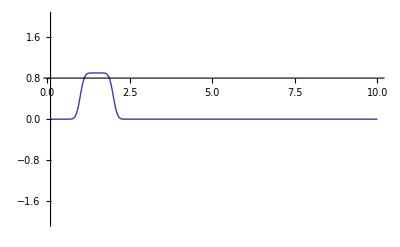

```mathematica
Plot[(n1/2)*(1-Erf[(x-e1)/(Sqrt[2]*s1)]) - (n2/2)*(1-Erf[(x-e2)/(Sqrt[2]*s2)])+(n3/2)*(1-Erf[(x-e3)/(Sqrt[2]*s3)]),{x,0.1,10},AxesOrigin->{0.1,0.8},PlotRange->{-2,2}]
```

New (13 Oct 2010) :

```mathematica
n=0.103;
e=0.37;
w=0.2;
```

```mathematica
c=1-(n/2)*(1-Erf[(0-e)/(Sqrt[2]*w)])
```

0.900312

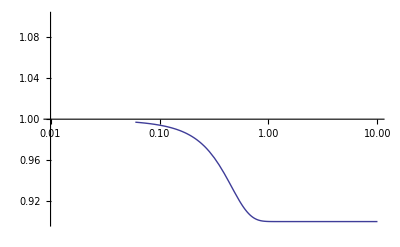

```mathematica
LogLinearPlot[(n/2)*(1-Erf[(x-e)/(Sqrt[2]*w)]) +c,{x,0.06,10},AxesOrigin->{0.01,1.0},PlotRange->{.9,1.1}]
```

```mathematica
Expand[(n/2)*(1-Erf[(x-e)/(Sqrt[2]*w)]) +c]
```

0.951812-0.0515 Erf[3.53553 (-0.37+x)]

```mathematica
LogLinearPlot[0.9518121478039482-0.0515 Erf[3.535533905932737 (-0.37+x)],{x,0.06,10},AxesOrigin->{0.01,1.0},PlotRange->{.9,1.1}]
```

-Graphics-

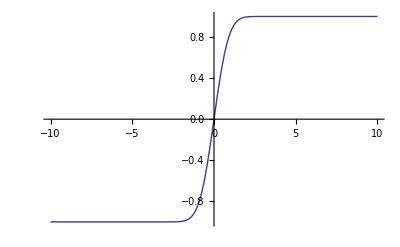

```mathematica
Plot[Erf[x],{x,-10,10},AxesOrigin->{0,0}]
```